```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,xcolor,bm,mhchem}","\\definecolor{darkgreen}{RGB}{0, 180, 0}"}];
```

## RHF-based resummation

### Taylor expansion vs Padé approximant

```mathematica
Exact[λ_,t_,U_]=1/2 (2 U-U λ-√(16 t^2+U^2 λ^2));
Taylor2[λ_,t_,U_]=Series[Exact[λ,t,U],{λ,0,2}]//Normal;
Taylor3[λ_,t_,U_]=Series[Exact[λ,t,U],{λ,0,3}]//Normal;
Taylor4[λ_,t_,U_]=Series[Exact[λ,t,U],{λ,0,4}]//Normal;
Taylor5[λ_,t_,U_]=Series[Exact[λ,t,U],{λ,0,5}]//Normal;
Taylor6[λ_,t_,U_]=Series[Exact[λ,t,U],{λ,0,6}]//Normal;
Pade01[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U],{λ,0,{0,1}}],t>0];
Pade11[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U],{λ,0,{1,1}}],t>0];
Pade22[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U],{λ,0,{2,2}}],t>0];
Pade33[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U],{λ,0,{3,3}}],t>0];
Pade44[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U],{λ,0,{4,4}}],t>0];
Pade55[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U],{λ,0,{5,5}}],t>0];
```

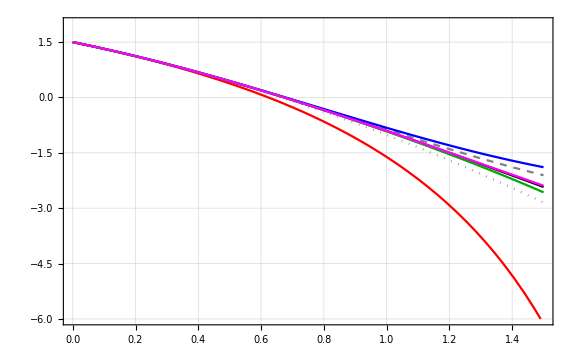

```mathematica
With[{U=3.5,t=1},Plot[{Exact[λ,t,U],Taylor2[λ,t,U],Taylor4[λ,t,U],Pade11[λ,t,U],Pade22[λ,t,U],Pade33[λ,t,U],Pade44[λ,t,U]},{λ,0,3/2},PlotRange->{{0,3/2},{-6,2}},PlotLabel->MaTeX["U/t = 3.5",FontSize->30],GridLines->Automatic,
PlotLegends->Placed[{MaTeX["\\text{Exact}",FontSize->20],MaTeX["\\text{2nd-order Taylor}",FontSize->20],MaTeX["\\text{4th-order Taylor}",FontSize->20],MaTeX["\\text{[1/1] Pad\\'e}",FontSize->20],MaTeX["\\text{[2/2] Pad\\'e}",FontSize->20],MaTeX["\\text{[3/3] Pad\\'e}",FontSize->20],MaTeX["\\text{[4/4] Pad\\'e}",FontSize->20]},Right],
PlotStyle->{{Black,Thick},{Gray,Dotted,Thick},{Gray,Dashed,Thick},{Red,Thick},{Blue,Thick},{Darker[Green],Thick},{Magenta,Thick}},
PlotTheme->"Scientific",FrameLabel->{MaTeX["\\lambda",FontSize->20],MaTeX["E_{-}(\\lambda)",FontSize->20]},ImageSize->Large,BaseStyle->20,FrameStyle->{Black,Thick},PlotRangePadding->0]
]
Export["PadeRMP35.pdf",%];
```

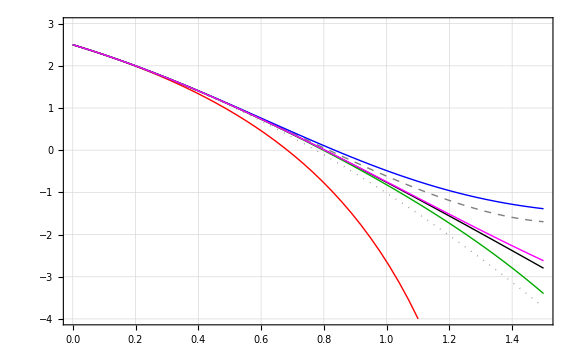

```mathematica
With[{U=4.5,t=1},Plot[{Exact[λ,t,U],Taylor2[λ,t,U],Taylor4[λ,t,U],Pade11[λ,t,U],Pade22[λ,t,U],Pade33[λ,t,U],Pade44[λ,t,U]},{λ,0,3/2},PlotRange->{{0,3/2},{-4,3}},PlotLabel->MaTeX["U/t = 4.5",FontSize->30],GridLines->Automatic,
PlotStyle->{{Black,Thick},{Gray,Dotted,Thick},{Gray,Dashed,Thick},{Red,Thick},{Blue,Thick},{Darker[Green],Thick},{Magenta,Thick}},
PlotTheme->"Scientific",FrameLabel->{MaTeX["\\lambda",FontSize->20],MaTeX["E_{-}(\\lambda)",FontSize->20]},ImageSize->Large,BaseStyle->20,FrameStyle->{Black,Thick},PlotRangePadding->0]
]
Export["PadeRMP45.pdf",%];
```

```mathematica
With[{t=1,U=3.5,λ=1},{Taylor2[λ,t,U],Taylor3[λ,t,U],Taylor4[λ,t,U],Taylor5[λ,t,U],Taylor6[λ,t,U],Exact[λ,t,U]}]
With[{t=1,U=3.5,λ=1},{Pade11[λ,t,U],Pade22[λ,t,U],Pade33[λ,t,U],Pade44[λ,t,U],Pade55[λ,t,U],Exact[λ,t,U]}]
```

{-1.01563,-1.01563,-0.86908,-0.86908,-0.925179,-0.907536}

{-1.61111,-0.821244,-0.919949,-0.905789,-0.907783,-0.907536}

```mathematica
With[{t=1,U=4.5,λ=1},{Taylor2[λ,t,U],Taylor3[λ,t,U],Taylor4[λ,t,U],Taylor5[λ,t,U],Taylor6[λ,t,U],Exact[λ,t,U]}]
With[{t=1,U=4.5,λ=1},{Pade11[λ,t,U],Pade22[λ,t,U],Pade33[λ,t,U],Pade44[λ,t,U],Pade55[λ,t,U],Exact[λ,t,U]}]
```

{-1.01563,-1.01563,-0.615173,-0.615173,-0.868584,-0.760399}

{-2.64286,-0.484456,-0.819289,-0.748661,-0.762771,-0.760399}

```mathematica
(4t)/U/.{t->1,U->3.5}
Abs[λ]/.Solve[Pade11[λ,t,U]^-1==0,λ]/.{t->1,U->3.5}
Abs[λ]/.Solve[Pade22[λ,t,U]^-1==0,λ]/.{t->1,U->3.5}
Abs[λ]/.Solve[Pade33[λ,t,U]^-1==0,λ]/.{t->1,U->3.5}
Abs[λ]/.Solve[Pade44[λ,t,U]^-1==0,λ]/.{t->1,U->3.5}
Abs[λ]/.Solve[Pade55[λ,t,U]^-1==0,λ]/.{t->1,U->3.5}
```

1.14286

{2.28571}

{2.28571,2.28571}

{4.01115,1.72543,1.72543}

{1.46894,1.46894,3.55664,3.55664}

{5.49076,1.35067,1.35067,2.49568,2.49568}

```mathematica
(4t)/U/.{t->1,U->4.5}
Abs[λ]/.Solve[Pade11[λ,t,U]^-1==0,λ]/.{t->1,U->4.5}//Sort
Abs[λ]/.Solve[Pade22[λ,t,U]^-1==0,λ]/.{t->1,U->4.5}//Sort
Abs[λ]/.Solve[Pade33[λ,t,U]^-1==0,λ]/.{t->1,U->4.5}//Sort
Abs[λ]/.Solve[Pade44[λ,t,U]^-1==0,λ]/.{t->1,U->4.5}//Sort
Abs[λ]/.Solve[Pade55[λ,t,U]^-1==0,λ]/.{t->1,U->4.5}//Sort
```

0.888889

{1.77778}

{1.77778,1.77778}

{1.342,1.342,3.11978}

{1.14251,1.14251,2.76628,2.76628}

{1.05052,1.05052,1.94108,1.94108,4.27059}

```mathematica
TableForm[{{With[{U=4,t=1},ComplexPlot3D[Exact[λ,t,U],{λ,-2ⅈ-2,2ⅈ+2},Mesh->{Range[0,5],Range[-Pi,Pi,Pi/4]},MeshFunctions->{Log[Abs[#2]]&,Arg[#2]&},PlotPoints->75]],
With[{U=4,t=1},ComplexPlot3D[Pade12[λ,t,U],{λ,-2ⅈ-2,2ⅈ+2},Mesh->{Range[0,5],Range[-Pi,Pi,Pi/4]},MeshFunctions->{Log[Abs[#2]]&,Arg[#2]&},PlotPoints->75]],
With[{U=4,t=1},ComplexPlot3D[Pade23[λ,t,U],{λ,-2ⅈ-2,2ⅈ+2},Mesh->{Range[0,5],Range[-Pi,Pi,Pi/4]},MeshFunctions->{Log[Abs[#2]]&,Arg[#2]&},PlotPoints->75]],
With[{U=4,t=1},ComplexPlot3D[Pade34[λ,t,U],{λ,-2ⅈ-2,2ⅈ+2},Mesh->{Range[0,5],Range[-Pi,Pi,Pi/4]},MeshFunctions->{Log[Abs[#2]]&,Arg[#2]&},PlotPoints->75]]
}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

### Quadratic approximants

```mathematica
QuadraticApproximant[dP_,dQ_,dR_]:=Module[{dE,c,P,Q,R,E},
dE=dP+dQ+dR+1;
If[dR≥0,
(P=∑_(k=0)^dP Subscript[p, k] λ^k;	Q=∑_(k=0)^dQ Subscript[q, k] λ^k/.Subscript[q, 0]->1;	R=∑_(k=0)^dR Subscript[r, k] λ^k;
E=Series[Exact[λ,t,U],{λ,0,dE}];
c=Solve[CoefficientList[Series[Q E^2-P E+R,{λ,0,dE}],λ]==0,Flatten[{Table[Subscript[p, k],{k,0,dP}],Table[Subscript[q, k],{k,1,dQ}],Table[Subscript[r, k],{k,0,dR}]}]]⟦1⟧;
Return[FullSimplify[{"["<>ToString[dP]<>"/"<>ToString[dQ]<>","<>ToString[dR]<>"]",
"n_bp = "<>ToString[Max[2dP,dQ+dR]],
1/(2Q)(P-√(P^2-4Q R)),1/(2Q)(P+√(P^2-4Q R))}/.c,t>0&&U>0]];
)
];
];
```

```mathematica
QA000[λ_,t_,U_]=QuadraticApproximant[0,0,0];
QA100[λ_,t_,U_]=QuadraticApproximant[1,0,0];
QA101[λ_,t_,U_]=QuadraticApproximant[1,0,1];
QA111[λ_,t_,U_]=QuadraticApproximant[1,1,1];
```

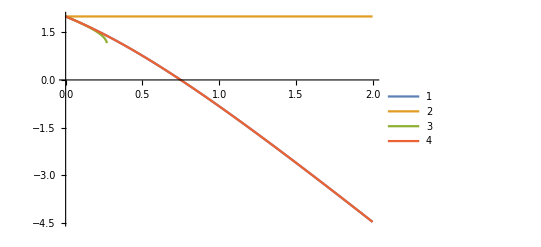

```mathematica
With[{U=4,t=1},Plot[{Exact[λ,t,U],QA000[λ,t,U]⟦3⟧,QA100[λ,t,U]⟦4⟧,QA101[λ,t,U]⟦3⟧},{λ,0,2},PlotLegends->Automatic]]
```

## UHF-based resummation

### Taylor expansion vs Padé approximant

```mathematica
Exact[λ_,t_,U_]=Table[Root[4 t^2 U^4 λ-4 t^2 U^4 λ^2+(2 U^4-8 t^2 U^2 λ-2 U^4 λ+4 t^2 U^2 λ^2) #1+(-3 U^2+2 U^2 λ) #1^2+#1^3&,k]/U,{k,3}];
Taylor2[λ_,t_,U_]=Series[Exact[λ,t,U]⟦1⟧,{λ,0,2}]//Normal;
Taylor4[λ_,t_,U_]=Series[Exact[λ,t,U]⟦1⟧,{λ,0,4}]//Normal;
Pade11[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U]⟦1⟧,{λ,0,{1,1}}],t>0];
Pade22[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U]⟦1⟧,{λ,0,{2,2}}],t>0];
Pade33[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U]⟦1⟧,{λ,0,{3,3}}],t>0];
Pade44[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U]⟦1⟧,{λ,0,{4,4}}],t>0];
Pade55[λ_,t_,U_]=FullSimplify[PadeApproximant[Exact[λ,t,U]⟦1⟧,{λ,0,{5,5}}],t>0];
```

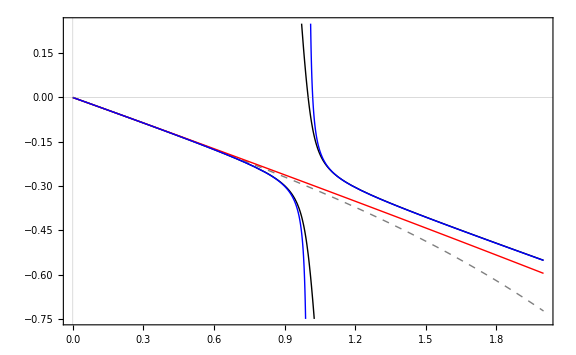

```mathematica
With[{U=7,t=1},Plot[{Exact[λ,t,U],Taylor4[λ,t,U],Pade11[λ,t,U],Pade22[λ,t,U]},{λ,0,2},
PlotLegends->Placed[{MaTeX["\\text{Exact}",FontSize->12],MaTeX["\\text{4th-order Taylor}",FontSize->12],MaTeX["\\text{[1/1] Pad\\'e}",FontSize->12],MaTeX["\\text{[2/2] Pad\\'e}",FontSize->12]},{Left,Bottom}],
PlotStyle->{{Black,Thick},{Gray,Dashed,Thick},{Red,Thick},{Blue,Thick},{Darker[Green],Thick},{Magenta,Thick}},
PlotTheme->"Scientific",FrameLabel->{MaTeX["\\lambda",FontSize->20],MaTeX["E(\\lambda)",FontSize->20]},ImageSize->Large,BaseStyle->16,PlotRange->{All,{-3/4,1/4}}]
]
```

```mathematica
Abs[λ]/.Solve[Pade22[λ,t,U]^-1==0,λ]/.{t->1,U->3.}//Sort
Abs[λ]/.Solve[Pade33[λ,t,U]^-1==0,λ]/.{t->1,U->3.}//Sort
λ/.Solve[Pade44[λ,t,U]^-1==0,λ]/.{t->1,U->3.}//Sort
λ/.Solve[Pade55[λ,t,U]^-1==0,λ]/.{t->1,U->3.}//Sort
```

{0.97448,17.4992}

{1.14138,10.4161,10.4161}

{-8.89987-14.6966 ⅈ,-8.89987+14.6966 ⅈ,1.06318-0.101549 ⅈ,1.06318+0.101549 ⅈ}

{-3.11598-7.52217 ⅈ,-3.11598+7.52217 ⅈ,1.11382-0.138662 ⅈ,1.11382+0.138662 ⅈ,20.3633}

```mathematica
Abs[λ]/.Solve[Pade22[λ,t,U]^-1==0,λ]/.{t->1,U->7.}//Sort
Abs[λ]/.Solve[Pade33[λ,t,U]^-1==0,λ]/.{t->1,U->7.}//Sort
Abs[λ]/.Solve[Pade44[λ,t,U]^-1==0,λ]/.{t->1,U->7.}//Sort
Abs[λ]/.Solve[Pade55[λ,t,U]^-1==0,λ]/.{t->1,U->7.}//Sort
```

{1.0003,590.011}

{1.00448,13.4257,369.459}

{1.00337,1.00337,28.4906,12494.2}

{1.00418,1.00418,2.31167,28.6962,10610.4}

```mathematica
{Pade22[λ,t,U],Pade33[λ,t,U],Pade44[λ,t,U],Pade55[λ,t,U]}/.{λ->1,t->1,U->3.}
{Pade22[λ,t,U],Pade33[λ,t,U],Pade44[λ,t,U],Pade55[λ,t,U]}/.{λ->1,t->1,U->7.}
```

{0.75,-1.10896,-0.853962,-0.972538}

{-17.9375,-1.49856,-0.335955,-0.355129}

### Quadratic approximants

```mathematica
QuadraticApproximant[dP_,dQ_,dR_]:=Module[{dE,c,P,Q,R,E},
dE=dP+dQ+dR+1;
If[dR≥0,
(P=∑_(k=0)^dP Subscript[p, k] λ^k;	Q=∑_(k=0)^dQ Subscript[q, k] λ^k/.Subscript[q, 0]->1;	R=∑_(k=0)^dR Subscript[r, k] λ^k;
E=Series[Exact[λ,t,U]⟦1⟧,{λ,0,dE}];
c=Solve[CoefficientList[Series[Q E^2-P E+R,{λ,0,dE}],λ]==0,Flatten[{Table[Subscript[p, k],{k,0,dP}],Table[Subscript[q, k],{k,1,dQ}],Table[Subscript[r, k],{k,0,dR}]}]]⟦1⟧;
Return[{"["<>ToString[dP]<>"/"<>ToString[dQ]<>","<>ToString[dR]<>"]",
"n_bp = "<>ToString[Max[2dP,dQ+dR]],
1/(2Q)(P-√(P^2-4Q R)),1/(2Q)(P+√(P^2-4Q R))}/.c];
)
];
];
```

```mathematica
QA000[λ_,t_,U_]=QuadraticApproximant[0,0,0];
QA100[λ_,t_,U_]=QuadraticApproximant[1,0,0];
QA101[λ_,t_,U_]=QuadraticApproximant[1,0,1];
QA111[λ_,t_,U_]=QuadraticApproximant[1,1,1];
QA211[λ_,t_,U_]=QuadraticApproximant[2,1,1];
QA212[λ_,t_,U_]=QuadraticApproximant[2,1,2];
QA222[λ_,t_,U_]=QuadraticApproximant[2,2,2];
QA322[λ_,t_,U_]=QuadraticApproximant[3,2,2];
QA323[λ_,t_,U_]=QuadraticApproximant[3,2,3];
QA333[λ_,t_,U_]=QuadraticApproximant[3,3,3];
(*QA433[λ_,t_,U_]=QuadraticApproximant[4,3,3]⟦3⟧;
QA443[λ_,t_,U_]=QuadraticApproximant[4,4,3]⟦3⟧;
QA444[λ_,t_,U_]=QuadraticApproximant[4,4,4]⟦3⟧;*)
```

```mathematica
{QA212[λ,t,U]⟦3;;4⟧,QA222[λ,t,U]⟦3;;4⟧,QA322[λ,t,U]⟦3;;4⟧,QA323[λ,t,U]⟦3;;4⟧,QA333[λ,t,U]⟦3;;4⟧,Exact[λ,t,U]}/.{t->1,U->3.,λ->1}
{QA212[λ,t,U]⟦3;;4⟧,QA222[λ,t,U]⟦3;;4⟧,QA322[λ,t,U]⟦3;;4⟧,QA323[λ,t,U]⟦3;;4⟧,QA333[λ,t,U]⟦3;;4⟧,Exact[λ,t,U]}/.{t->1,U->7.,λ->1}
```

{{-1.01009,-0.0601142},{-1.00553,-0.100578},{-1.00568,-0.107267},{-0.999732,-0.0155386},{-0.999664,-0.0144505},{-1.,4.,0.+0. ⅈ}}

{{-0.534723,-0.00576841},{-0.534628,-0.00593924},{0.0119191,-0.524726},{-0.531021,-0.000218185},{-0.531026,-0.000216337},{-0.531129,7.53113,0.+0. ⅈ}}

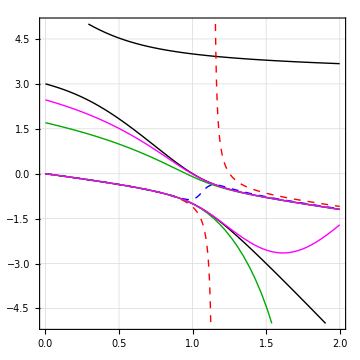

```mathematica
With[{U=3,t=1},Plot[{Exact[λ,t,U],Pade33[λ,t,U],Pade44[λ,t,U],QA222[λ,t,U]⟦3;;4⟧,QA333[λ,t,U]⟦3;;4⟧},{λ,0,2},
PlotLegends->Placed[{MaTeX["\\text{Exact}",FontSize->12],MaTeX["\\text{[3/3] Pad\\'e}",FontSize->12],MaTeX["\\text{[4/4] Pad\\'e}",FontSize->12],MaTeX["\\text{[2/2,2] Quadratic}",FontSize->12],MaTeX["\\text{[3/3,3] Quadratic}",FontSize->12]},{Left,Bottom}],GridLines->Automatic,
PlotStyle->{{Black,Thick},{Red,Dashed,Thick},{Blue,Dashed,Thick},{Darker[Green],Thick},{Magenta,Thick}},AspectRatio->1,
PlotTheme->"Scientific",FrameLabel->{MaTeX["\\lambda",FontSize->20],MaTeX["E(\\lambda)",FontSize->20]},ImageSize->Medium,BaseStyle->16,PlotRange->{All,{-5,5}},FrameStyle->{Black,Thick},PlotRangePadding->0]
]
Export["QuadUMP.pdf",%];
```

```mathematica
Abs[λ]/.NSolve[QA101[λ,t,U]⟦3⟧==QA101[λ,t,U]⟦4⟧/.{U->7,t->1.},λ]//Sort
Abs[λ]/.NSolve[QA111[λ,t,U]⟦3⟧==QA111[λ,t,U]⟦4⟧/.{U->7,t->1.},λ]//Sort
Abs[λ]/.NSolve[QA211[λ,t,U]⟦3⟧==QA211[λ,t,U]⟦4⟧/.{U->7,t->1.},λ]//Sort
Abs[λ]/.NSolve[QA212[λ,t,U]⟦3⟧==QA212[λ,t,U]⟦4⟧/.{U->7,t->1.},λ]//Sort
Abs[λ]/.NSolve[QA222[λ,t,U]⟦3⟧==QA222[λ,t,U]⟦4⟧/.{U->7,t->1.},λ]//Sort
Abs[λ]/.NSolve[QA322[λ,t,U]⟦3⟧==QA322[λ,t,U]⟦4⟧/.{U->7,t->1.},λ]//Sort
Abs[λ]/.NSolve[QA323[λ,t,U]⟦3⟧==QA323[λ,t,U]⟦4⟧/.{U->7,t->1.},λ]//Sort
Abs[λ]/.NSolve[QA333[λ,t,U]⟦3⟧==QA333[λ,t,U]⟦4⟧/.{U->7,t->1.},λ]//Sort
```

{0.840964,1.54411}

{0.798895,1.40798}

{0.825799,1.37517,3.90172,3.90172}

{1.0031,1.0031,24.9138,24.9138}

{1.0031,1.0031,24.8444,24.8444}

{1.00106,1.00106,10.2523,10.2523,26.2027,26.2027}

{1.00239,1.00239,1.58643,1.58643,24.9358,24.9358}

{1.00239,1.00239,1.60213,1.60213,24.9369,24.9369}

```mathematica
With[{U=4,t=1},ListPlot[{Table[{λ,Exact[λ,t,U]},{λ,0,2,0.1}],Table[{λ,QA444[λ,t,U]},{λ,0,2,0.1}]},,PlotLegends->Automatic]]
```